```mathematica
Get["path-integrals.m"];
Kimura[x_,y_,t_,n_]:= Module[{m},Sum[4*(2*m+1)*x*(1-x)/(m*(m+1))*GegenbauerC[m-1,3/2,1-2*x]*GegenbauerC[m-1,3/2,1-2*y]*Exp[-1/2*m*(m+1)*t],{m,1,n}]
]
haywardVGMinus4 = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50] + Sum[(2 Ne^2 α Λ / W^2)^j pints[[j]][[1]],{j,1,5}]);
haywardVGMinus3 = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50] + Sum[(2 Ne^2 α Λ / W^2)^j pints[[j]][[2]],{j,1,5}]);
haywardVGMinus2 = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50] + Sum[(2 Ne^2 α Λ / W^2)^j pints[[j]][[3]],{j,1,5}]);
haywardVGMinus1 = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50] + Sum[(2 Ne^2 α Λ / W^2)^j pints[[j]][[4]],{j,1,5}]);
Clear[pints]
```

```mathematica
(*XXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXX*)
(*XXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXX VG XXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXX*)
(*XXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXX*)
```

```mathematica
fitVar = 1;
time = 0.05;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
start= 0.1;
```

0.984642

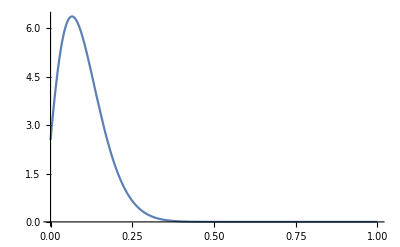

```mathematica
neutAUC = NIntegrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}], {y,0,1}]
Plot[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}], {y,0,1}]
```

```mathematica
pNeutFix = 1- neutAUC;
tmp = Integrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}],{y, start+Ψ,1}];
```

```mathematica
thresh = Solve[tmp == 1-sigCutoff && 0<Ψ<1, {Ψ}, Reals];
If[Length[thresh] != 1,Throw[{}]];
```

```mathematica
Ψ = Ψ /. thresh;
Ψ = Ψ[[1]];
Print[Ψ];
```

0.192309

```mathematica
pNeutFix +  NIntegrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}],{y, 0,start+Ψ}]
```

0.989995

```mathematica
(***********************)
(******* VG = 0.1 *******)
(***********************)
```

```mathematica
Clear[genVar];
genVar = 0.1;
```

```mathematica
Do[Clear[blah, pintAUC, pintDetected, numAUC, numDetected,statDist];
Print[selCoef,":"];
blah = NDSolve[{D[f[y,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[y(1-y)f[y,t],y] + 1/2 D[y(1-y)f[y,t],{y,2}],
f[y,0]==Evaluate[PDF[TriangularDistribution[{(start - 0.001),(start + 0.001)},start],y]]} /. {α->selCoef,Λ->jumpSize, Ne -> selectedNe, VG -> genVar, W->fitVar},
f,{y,0,1},{t,0,0.25},MaxStepSize->.00025];
pintAUC = NIntegrate[Evaluate[haywardVGMinus1/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],{y, 0,1}];
pintDetected = NIntegrate[Evaluate[haywardVGMinus1/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],{y, start+Ψ,1}];
Print["pint:",pintAUC, " xxxx ", pintDetected];
numAUC = NIntegrate[Evaluate[{f[y, time]} /. blah],{y,0,1}][[1]][[1]];
numDetected= NIntegrate[Evaluate[{f[y, time]} /. blah],{y,start + Ψ,1}][[1]][[1]];
Print["num:",numAUC, " xxxx ", numDetected];
statDist = 1/2 NIntegrate[Abs[Evaluate[haywardVGMinus1/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}] - Evaluate[{f[y, time]} /. blah]],{y,0,1}];
Print[statDist];
Export[StringJoin["pDetection_","alpha",ToString[selCoef], "_VG",ToString[genVar],".csv"], {{selCoef,genVar,start,time, Ψ,pintAUC,pintDetected, numAUC, numDetected, statDist}}, "csv"],
{selCoef, {0,0.001,0.005,0.01,0.015,0.02}}
]
```

0:

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

pint:0.984642 xxxx 0.0100054

num:0.98464 xxxx 0.0100065

{{8.73514×10^-6}}

0.001:

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

```mathematica
(************************)
(******* VG = 0.01 *******)
(************************)
```

```mathematica
Clear[genVar];
genVar = 0.01;
```

```mathematica
Do[Clear[blah, pintAUC, pintDetected, numAUC, numDetected,statDist];
Print[selCoef,":"];
blah = NDSolve[{D[f[y,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[y(1-y)f[y,t],y] + 1/2 D[y(1-y)f[y,t],{y,2}],
f[y,0]==Evaluate[PDF[TriangularDistribution[{(start - 0.001),(start + 0.001)},start],y]]} /. {α->selCoef,Λ->jumpSize, Ne -> selectedNe, VG -> genVar, W->fitVar},
f,{y,0,1},{t,0,0.25},MaxStepSize->.00025];
pintAUC = NIntegrate[Evaluate[haywardVGMinus2/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],{y, 0,1}];
pintDetected = NIntegrate[Evaluate[haywardVGMinus2/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],{y, start+Ψ,1}];
Print["pint:",pintAUC, " xxxx ", pintDetected];
numAUC = NIntegrate[Evaluate[{f[y, time]} /. blah],{y,0,1}][[1]][[1]];
numDetected= NIntegrate[Evaluate[{f[y, time]} /. blah],{y,start + Ψ,1}][[1]][[1]];
Print["num:",numAUC, " xxxx ", numDetected];
statDist = 1/2 NIntegrate[Abs[Evaluate[haywardVGMinus2/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}] - Evaluate[{f[y, time]} /. blah]],{y,0,1}];
Print[statDist];
Export[StringJoin["pDetection_","alpha",ToString[selCoef], "_VG",ToString[genVar],".csv"], {{selCoef,genVar,start,time, Ψ,pintAUC,pintDetected, numAUC, numDetected, statDist}}, "csv"],
{selCoef, {0,0.001,0.005,0.01,0.015,0.02}}
]
```

0.015:

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

pint:0.996251 xxxx 0.0921916

num:0.996268 xxxx 0.0922072

```mathematica
(***********************)
(******* VG = 0.001 *******)
(***********************)
```

```mathematica
Clear[genVar];
genVar = 0.001;
```

```mathematica
Do[Clear[blah, pintAUC, pintDetected, numAUC, numDetected, statDist];
Print[selCoef,":"];
blah = NDSolve[{D[f[y,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[y(1-y)f[y,t],y] + 1/2 D[y(1-y)f[y,t],{y,2}],
f[y,0]==Evaluate[PDF[TriangularDistribution[{(start - 0.001),(start + 0.001)},start],y]]} /. {α->selCoef,Λ->jumpSize, Ne -> selectedNe, VG -> genVar, W->fitVar},
f,{y,0,1},{t,0,0.25},MaxStepSize->.00025];
pintAUC = NIntegrate[Evaluate[haywardVGMinus3/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],{y, 0,1}];
pintDetected = NIntegrate[Evaluate[haywardVGMinus3/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],{y, start+Ψ,1}];
Print["pint:",pintAUC, " xxxx ", pintDetected];
numAUC = NIntegrate[Evaluate[{f[y, time]} /. blah],{y,0,1}][[1]][[1]];
numDetected= NIntegrate[Evaluate[{f[y, time]} /. blah],{y,start + Ψ,1}][[1]][[1]];
Print["num:",numAUC, " xxxx ", numDetected];
statDist = 1/2 NIntegrate[Abs[Evaluate[haywardVGMinus3/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}] - Evaluate[{f[y, time]} /. blah]],{y,0,1}];
Print[statDist];
Export[StringJoin["pDetection_","alpha",ToString[selCoef], "_VG",ToString[genVar],".csv"], {{selCoef,genVar,start,time, Ψ,pintAUC,pintDetected, numAUC, numDetected,statDist}}, "csv"],
{selCoef, {0,0.001,0.005,0.01,0.015,0.02}}
]
```

0:

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

pint:0.984642 xxxx 0.0100054

num:0.98464 xxxx 0.0100065

{{8.73514×10^-6}}

0.001:

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

pint:0.986091 xxxx 0.0124581

num:0.986089 xxxx 0.0124593

{{8.96364×10^-6}}

0.005:

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

General::stop: Further output of NDSolve::mxsst will be suppressed during this calculation.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

General::stop: Further output of NDSolve::bcart will be suppressed during this calculation.

pint:0.990785 xxxx 0.028104

num:0.990783 xxxx 0.0281061

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0541711}. NIntegrate obtained 0.0000197542 and 6.30258×10^-11 for the integral and error estimates.

{{9.87709×10^-6}}

0.01:

pint:0.994678 xxxx 0.067547

num:0.994677 xxxx 0.0675506

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.253891}. NIntegrate obtained 0.0000219997 and 5.74241×10^-11 for the integral and error estimates.

{{0.0000109998}}

0.015:

pint:0.99692 xxxx 0.139684

num:0.997039 xxxx 0.139755

{{0.0000597845}}

0.02:

pint:0.971453 xxxx 0.227821

num:0.998413 xxxx 0.25097

{{0.0135296}}

```mathematica
(***********************)
(******* VG = 0.0001 *******)
(***********************)
```

```mathematica
Clear[genVar];
genVar = 0.0001;
```

```mathematica
Do[Clear[blah, pintAUC, pintDetected, numAUC, numDetected,statDist];
Print[selCoef,":"];
blah = NDSolve[{D[f[y,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[y(1-y)f[y,t],y] + 1/2 D[y(1-y)f[y,t],{y,2}],
f[y,0]==Evaluate[PDF[TriangularDistribution[{(start - 0.001),(start + 0.001)},start],y]]} /. {α->selCoef,Λ->jumpSize, Ne -> selectedNe, VG -> genVar, W->fitVar},
f,{y,0,1},{t,0,0.25},MaxStepSize->.00025];
pintAUC = NIntegrate[Evaluate[haywardVGMinus4/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],{y, 0,1}];
pintDetected = NIntegrate[Evaluate[haywardVGMinus4/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],{y, start+Ψ,1}];
Print["pint:",pintAUC, " xxxx ", pintDetected];
numAUC = NIntegrate[Evaluate[{f[y, time]} /. blah],{y,0,1}][[1]][[1]];
numDetected= NIntegrate[Evaluate[{f[y, time]} /. blah],{y,start + Ψ,1}][[1]][[1]];
Print["num:",numAUC, " xxxx ", numDetected];
statDist = 1/2 NIntegrate[Abs[Evaluate[haywardVGMinus4/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}] - Evaluate[{f[y, time]} /. blah]],{y,0,1}];
Print[statDist];
Export[StringJoin["pDetection_","alpha",ToString[selCoef], "_VG",ToString[genVar],".csv"], {{selCoef,genVar,start,time, Ψ,pintAUC,pintDetected, numAUC, numDetected,statDist}}, "csv"],
{selCoef, {0,0.001,0.005,0.01,0.015,0.02}}
]
```

0:

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

pint:0.984642 xxxx 0.0100054

num:0.98464 xxxx 0.0100065

{{8.73514×10^-6}}

0.001:

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

pint:0.986112 xxxx 0.0125228

num:0.98611 xxxx 0.012524

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.187484}. NIntegrate obtained 0.000017935 and 7.90624×10^-11 for the integral and error estimates.

{{8.96752×10^-6}}

0.005:

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

General::stop: Further output of NDSolve::mxsst will be suppressed during this calculation.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

General::stop: Further output of NDSolve::bcart will be suppressed during this calculation.

pint:0.990858 xxxx 0.0287467

num:0.990856 xxxx 0.0287489

{{9.89393×10^-6}}

0.01:

pint:0.994765 xxxx 0.0701216

num:0.994765 xxxx 0.0701252

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0742032}. NIntegrate obtained 0.0000228429 and 2.07374×10^-10 for the integral and error estimates.

{{0.0000114214}}

0.015:

pint:0.99914 xxxx 0.148455

num:0.997115 xxxx 0.14621

{{0.00150262}}

0.02:

pint:4.04168 xxxx 3.31902

num:0.998469 xxxx 0.263007

{{1.56663}}

```mathematica
(**********************************************************************************)
```

```mathematica
selCoef = 0.02
```

0.02

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

{{f→InterpolatingFunction[{{0., 1.}, {0., 0.25}}, <>]}}

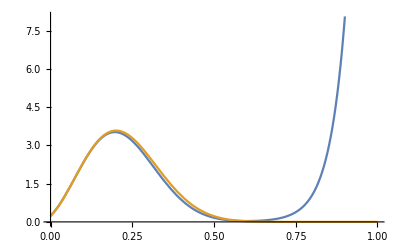

```mathematica
blah = NDSolve[{D[f[y,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[y(1-y)f[y,t],y] + 1/2 D[y(1-y)f[y,t],{y,2}],
f[y,0]==Evaluate[PDF[TriangularDistribution[{(start - 0.001),(start + 0.001)},start],y]]} /. {α->selCoef,Λ->jumpSize, Ne -> selectedNe, VG -> genVar, W->fitVar},
f,{y,0,1},{t,0,0.25},MaxStepSize->.00025]
Plot[{Evaluate[haywardVGMinus4/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],
f[y,time] /. blah} ,{y, 0,1}]
```

```mathematica
pintAUC = NIntegrate[Evaluate[haywardVGMinus4/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],{y, 0,1}]
pintDetected = NIntegrate[Evaluate[haywardVGMinus4/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],{y, start+Ψ,1}]
```

4.04168

3.31902

```mathematica
4.041679425143229 - 3.3190237915877043
pintAUC - pintDetected
```

0.722656

0.722656

```mathematica
Clear[selCoef]
```